```mathematica
CloudConnect["tarek.tohme@ens.psl.eu"]
```

tarek.tohme@ens.psl.eu

```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica-nbs"];
Get["ctmc`"]
```

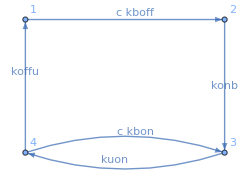

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Pure ligand, 1 binding site ***)

(*Edge lists and weights*)
edges1={{1,2},{2,3},{3,4},{4,3},{4,1}};
weights1={c*kboff,konb,kuon,c*kbon,koffu};
nstates1 = 4;
nedges1 = 5;

(*Plot the circuit*)
edgeList=Table[edges1[[i,1]]->edges1[[i,2]],{i,1,nedges1}];
g=Graph[edges1,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights1)[[i]],0.55],{i,1,nedges1}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{4,1},{3,2}}}]
```

```mathematica
Q1= RateMatrix[edges1, weights1, nstates1];
ss1 = SteadyStateProbabilities[Q1];
(*Mean first passage times*)
meanToff=MeanFirstPassageTimes[Q1][[1,3]][[1]];
meanTon = MeanFirstPassageTimes[Q1][[3,1]][[1]];
tau = meanToff + meanTon;

(*Variance of first passage times*)
varToff = FullSimplify[VarianceFirstPassageTimes[Q1][[1,3]]][[1]][[1]];
varTon = FullSimplify[VarianceFirstPassageTimes[Q1][[3,1]]][[1]][[1]];
```

```mathematica
(*Validating the Laplace transform FPT means and variances*)
Foff = LaplaceTransformFPT[Q1,s1][[1,3]][[1]];
Fon = LaplaceTransformFPT[Q1,s2][[3,1]][[1]];
meanToffLt = FullSimplify[-With[{s1=0},Evaluate[D[Foff,{s1,1}]]]];
meanTonLt = FullSimplify[-With[{s2=0},Evaluate[D[Fon,{s2,1}]]]];
varToffLt = FullSimplify[With[{s1=0},Evaluate[D[Foff,{s1,2}]]]-meanToffLt^2];
varTonLt = FullSimplify[With[{s2=0},Evaluate[D[Fon,{s2,2}]]]-meanTonLt^2];

On[Assert];
Assert[meanToffLt==meanToff]
Assert[meanTonLt==meanTon]
Assert[varToffLt==varToff]
Assert[varTonLt==varTon]
```

```mathematica
(*MM estimators*)
cHatOff = c/.Solve[meanToff==sampleToff,c][[1]];
cHatOn = c/.Solve[meanTon==sampleTon,c][[1]];

(*Variances of estimators*)
VarCHatOff = Simplify[With[{sampleToff = meanToff}, Evaluate[D[cHatOff, {sampleToff,1}]^2]]*varToff];
VarCHatOn = Simplify[With[{sampleTon = meanTon}, Evaluate[D[cHatOn, {sampleTon,1}]^2]]*varTon];
```

```mathematica
(*Concentration-rescaled Fisher information rates*)
dotFoff = FullSimplify[c^2 / (tau*VarCHatOff)];
dotFon = FullSimplify[c^2 / (tau*VarCHatOn)];
dotF = dotFoff + dotFon;
```

```mathematica
FullSimplify[dotFoff]
```

(c kboff koffu konb^3 kuon)/((c^2 kboff^2+konb^2) (c kboff (c kbon+koffu) konb+koffu konb kuon+c kboff (koffu+konb) kuon))

```mathematica
(*Maximize Fisher information rate*)
NMaximize[{With[{c=50},Evaluate[dotFoff]],0<kboff<0.0888,0<konb<5,0<kuon<5,0<kbon<0.0888,0<koffu<5 },{kboff,konb,kuon,kbon,koffu}]
```

{0.8,{kboff→0.05,konb→5.,kuon→5.,kbon→-9.9875×10^-9,koffu→5.}}

```mathematica
(* tests *)
With[{c=1,kboff=1, konu=1, kbon=1, koffu=1, kuoff=1, konb=1, kuon=1, koffb=1},Evaluate[meanToffLt]]
```

2

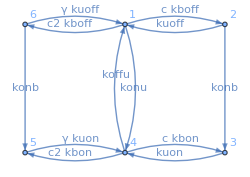

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
edges3={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},{4,5},
	    {5,4},{6,5},{4,1},{2,3},{1,4},{3,2},{5,6}};
weights3={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu,koffb,koffb};
Q3 = RateMatrix[edges3, weights3, nstates2];
```

```mathematica
LogSpecificity[c,ω,γ,{kboff->kdl,konb->ϵ,kuon->kmax,kbon->0,koffu->kmax,kuoff->kmax, konu->kmax,koffb->0},edges3]
```

Log[(c kdl kmax γ^2 ϵ+c kdl γ ϵ^2)/(c kdl ϵ (kmax+ϵ) ω)]+Log[ω/γ]

```mathematica
Simplify[%,{ω>=0, γ>=0}]
```

Log[(kmax γ+ϵ)/(kmax+ϵ)]

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {6,1,2};
onStates = {5,4,3};
Foff1on = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = Foff1on[[3]][[1]]*F31 +Foff1on[[2]][[1]]*F41 + Foff1on[[1]][[1]]*F51; (*F1off[[2]][[1]]*F41 +*)
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];

(*Covariance matrix*)
Σx = Simplify[{{varToffLt,covTonToff},{covTonToff,varTonLt}},assum];
```

```mathematica
(*MM estimators*)
cHatOffSym =Simplify[c/.Solve[meanToffLt==sampleToff,c][[1]],assum];
cHatOnSym = FullSimplify[c/.Solve[meanTonLt==sampleTon,c][[2]],assum];

(*Jacobian*)
dcHatOff=Simplify[With[{sampleToff=meanToffLt},Evaluate[D[cHatOffSym, {sampleToff,1}]]],assum];
dcHatOn=Simplify[With[{sampleTon=meanTonLt},Evaluate[D[cHatOnSym, {sampleTon,1}]]],assum];
delf = {{dcHatOff,0},{0,dcHatOn }};
```

```mathematica
(*Covariance matrix of estimators*)
Σy = delfᵀ.Σx.delf;
```

```mathematica
(*Combined estimator and its variance*)
σ2off = Σy[[1,1]];
σ2on = Σy[[2,2]];
Cov = Σy[[1,2]];
ρ = Cov/(σ2off*σ2on);

cHat = (cHatOffSym*(σ2on-Cov) + cHatOnSym*(σ2off-Cov))/(σ2off + σ2on - 2Cov);
σ2 = (σ2on*σ2off - Cov^2)/(σ2off + σ2on - 2Cov);

(*Concentration-rescaled Fisher information rates*)
Foff = c^2/ (τ*σ2off*(1-ρ)^2);
Fon = c^2/ (τ*σ2on*(1-ρ)^2);
Fcross = -2*c^2*ρ/(τ*Sqrt[σ2off*σ2on]*(1-ρ)^2);
Fcomb = c^2/ (τ*σ2);
F[c_,c2_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_] := Evaluate[Fcomb];

(*G[c_,c2_,γ_,lnkboff_,lnkonb_,lnkuon_,lnkbon_,lnkoffu_,lnkuoff_,lnkonu_]:=F[c,c2,γ,Exp[lnkboff],Exp[lnkonb],Exp[lnkuon],Exp[lnkbon],Exp[lnkoffu],Exp[lnkuoff],Exp[lnkonu]];

H[c_,c2_,γ_,logrates_]:=Module[{kboff,konb,kuon,kbon,koffu,kuoff,konu},
{kboff,konb,kuon,kbon,koffu,kuoff,konu} = Table[Exp[logrates[[i]][[2]]],{i,1,Length[logrates]}];
F[c,c2,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu]]*)
```

```mathematica
F[10,0.01,0.1,0.05,5,5,0.0001,5,0.0001,0.0001]
```

0.379957

```mathematica
lnkmin = -5;
lnkmax = Log[5];
lnkdifflim = Log[0.0888];
cvals = Table[10.^x, {x,Subdivide[-2.5,2.5,30]}];
c2vals = Table[10.^x, {x,Subdivide[-2,3,30]}];
G[100,0,10,lnkmax-2.-Log[100], lnkmax,lnkmax,lnkmin,lnkmax,lnkmin,-5]
```

0.463464

```mathematica
(*Maximize*)
results = Table[{x,y,NMaximize[{G[c,c2,γ,lnkboff,lnkonb,lnkuon,lnkbon,lnkoffu,lnkuoff,lnkonu]/.{c->x,c2->y,γ->10},lnkmin<lnkboff<lnkdifflim,
lnkmin<lnkonb<lnkmax,
lnkmin<lnkuon<lnkmax,
lnkmin<lnkbon<lnkdifflim,
lnkmin<lnkoffu<lnkmax,
lnkmin<lnkuoff<lnkmax,
lnkmin<lnkonu<lnkmax},
{lnkboff,lnkonb,lnkuon,lnkbon,lnkoffu,lnkuoff,lnkonu},
Method->"DifferentialEvolution"]},{x, cvals},{y, cvals}]
```

```mathematica
(*Saving data*)
datafile = FileNameJoin[{$HomeDirectory},".julia/dev/LLROpt/mathematica-nbs/data/20250327/max-F-vs-c-vs-c2-30by30.wl"]
(*Save[file, results]*)
```

/home/tohme/.julia/dev/LLROpt/mathematica-nbs/data/20250327/max-F-vs-c-vs-c2-30by30.wl

```mathematica
(*Loading data*)
results = Get[datafile];
```

```mathematica
Table[Exp[results[[1,1]][[3]][[2]][[i]][[2]]], {i,1,7}]
```

{0.0888,5.,0.0677467,0.0888,5.,0.00673795,0.00673795}

```mathematica
(*Plots*)
k = 30;
cvals = Table[10.^x, {x,Subdivide[-2.5,2.5,k]}];
wvals = Table[10.^x, {x,Subdivide[-2,3,k]}];
cticks =Transpose[{Round[Subdivide[k,10]]+1,Subdivide[-2.5,2.5,10]}]; 
wticks = Transpose[{Round[Subdivide[k,10]]+1,Round[Subdivide[-2.,3.,10]]}];
moddata = Table[H[cvals[[i]],wvals[[j]],10,results[[i,j]][[3]][[2]]],{i,1,k},{j,1,k}];
```

```mathematica
fig2 = With[{g = GrayLevel[1-#] &},
ListDensityPlot[moddataᵀ,
InterpolationOrder->0,(*Controls smoothing:0=none,higher values=smoother interpolation*)
ColorFunction->g,
Frame->True,(*Use a framed plot to enable axis labels*)
FrameLabel->{"log(c_0)","log(c')"},(*Label your axes*)
LabelStyle->13,
FrameTicks->{
{wticks[[1 ;; ;; 2]],Automatic},
{cticks[[2 ;; ;; 2]],Automatic}
},
(*ScalingFunctions->{"Log"},*)
PlotLegends->BarLegend[{g, {Min[moddata],Max[moddata]}},LegendLabel->Placed["(Ḟ)_on/Ḟ",Right],LegendMarkerSize->200],(*Add a colorbar that matches the ColorFunction*)
ImageSize->250
]]
```

-Graphics-

```mathematica
dir = ".julia/dev/LLROpt/mathematica-nbs";
datadir = FileNameJoin[dir,"data"];
plotdir = FileNameJoin[dir,"plots"];
date = "20250327";
datafile = FileNameJoin[{$HomeDirectory},datadir, date, fname];
plotfile=FileNameJoin[{$HomeDirectory},plotdir, date, "max-linFonoverF-vs-c-vs-w30x30.pdf"];
Export[plotfile,fig2];
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*** Tests ***)
```

```mathematica
c2=1;
kboff=1;
konb=1;
kuon=1;
kbon=1;
koffu=4.5;
kuoff=1;
konu=1;
γ=1;
P31 = Simplify[InverseLaplaceTransform[F31,{s2},{t2}]];
P41 = Simplify[InverseLaplaceTransform[F41,{s2},{t2}]];
P51 = Simplify[InverseLaplaceTransform[F51,{s2},{t2}]];
```

```mathematica
P13 = Simplify[InverseLaplaceTransform[Foff1on[[3]][[1]],{s1},{t1}]];
P14 = Simplify[InverseLaplaceTransform[Foff1on[[2]][[1]],{s1},{t1}]];
P15 = Simplify[InverseLaplaceTransform[Foff1on[[1]][[1]],{s1},{t1}]];
```

```mathematica
With[{c=1,c2=1,kboff=1,konb=1,kuon=1,kbon=1,koffu=1,kuoff=1,konu=1, γ=1,t2=1.},Evaluate[P31]]
With[{c=1,c2=1,kboff=1,konb=1,kuon=1,kbon=1,koffu=1,kuoff=1,konu=1, γ=1,t2=1.},Evaluate[P41]]
With[{c=1,c2=1,kboff=1,konb=1,kuon=1,kbon=1,koffu=1,kuoff=1,konu=1, γ=1,t2=1.},Evaluate[P51]]

With[{c=1,c2=1,kboff=1,konb=1,kuon=1,kbon=1,koffu=1,kuoff=1,konu=1, γ=1,t1=1.},Evaluate[P13]]
With[{c=1,c2=1,kboff=1,konb=1,kuon=1,kbon=1,koffu=1,kuoff=1,konu=1, γ=1,t1=1.},Evaluate[P14]]
With[{c=1,c2=1,kboff=1,konb=1,kuon=1,kbon=1,koffu=1,kuoff=1,konu=1, γ=1,t1=1.},Evaluate[P15]]
```

0.213909

0.180536

0.213909

0.116521

0.134837

0.116521

```mathematica
rates={c>0,c2>0,γ>0,kboff>0,konb>0,kuon>0,kbon>0,koffu>0,kuoff>0,konu>0};
assum=And@@rates;

kmax =5.;
kmin=0.00001;
kdl=0.0888;
expr0 = Simplify[FoffOn];
expr1=Together[expr0]//Cancel;
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2];
(*exprS12PartEval = exprS12 /.{konb->kmax,kuon->kmax, koffu->kmax,kboff->kdl,kbon->kmin,konu->kmin,kuoff->kmax,c2->0,γ->10}*)
exprS12PartEval = exprS12 /.{c2->10.,γ->10.,konb->5.,koffu->5.,kuon->5.};
```

```mathematica
exprS12PartEvalSimpl = Simplify[exprS12PartEval]
```

(kboff (31250.+6250. s1+6250. s2+1250. s1 s2+kuoff (6250.+1250. s2)+c (3125.+625. s1+62.5 s2+12.5 s1 s2+kuoff (6250.+125. s2)))+konu (3125.+687.5 s2+12.5 s2^2+s1^2 (125.+27.5 s2+0.5 s2^2)+kuoff^2 (1250.+275. s2+5. s2^2)+s1 (1250.+275. s2+5. s2^2)+kuoff (6875.+1512.5 s2+27.5 s2^2+s1 (1375.+302.5 s2+5.5 s2^2))))/(((konu+s1) (2.5+1. kuoff^2+1. s1+0.1 s1^2+kuoff (5.5+1.1 s1))+kboff (25.+5. kuoff+10. s1+1. kuoff s1+1. s1^2+c (2.5+5. kuoff+1. s1+1. kuoff s1+0.1 s1^2))) (1250.+(525.+(50.+50. c) kbon) s2+(60.+(10.+c) kbon) s2^2+s2^3))

```mathematica
Pjoint=InverseLaplaceTransform[exprS12PartEvalSimpl,{s1,s2},{t1,t2},Assumptions->assum];(*~35s*)
```

```mathematica
d2LogPjoint =D[Log[Pjoint],{c,2}];
integrand = Pjoint *d2LogPjoint ;
```

```mathematica
(*Score function of the Laplace before inverting it*)
d2LogFjoint=Simplify[D[Log[exprS12PartEvalSimpl],{c,2}]];
```

```mathematica
expr1=Together[d2LogFjoint]//Cancel;
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2];
```

$Aborted

```mathematica
integrandAlt=InverseLaplaceTransform[d2LogFjoint,{s1,s2},{t1,t2},Assumptions->assum];
```

$Aborted

```mathematica
Clear[PjointPartEval]
Clear[d2LogPjointPartEval]
Clear[integrand]
```

```mathematica
PjointPartEval=Pjoint/.{konb->kmax,kuon->kmax, koffu->kmax,kboff->kdl,kbon->kmin,konu->kmin,kuoff->kmax};(*0.3s*)
```

```mathematica
PjointPartEval /.{c->1.,t1->1., t2->1.}
```

0.00919849

```mathematica
PjointPartEvalC=Compile[{{t1,_Real},{t2,_Real},{c,_Real}},
Evaluate[PjointPartEval],
CompilationTarget->"C",
RuntimeOptions->"Speed"](*6s*)
```

2     3                                                                                     2     3
                                           t2 Root[1250. + (525.001 + 0.0005 c) #1 + (60.0001 + 0.00001 c) #1  + #1  & , 2] + t1 Root[44.4055 + 24.42 c + (563.321 + 5.328 c) #1 + (65.888 + 0.0888 c) #1  + #1  & , 2]                                           3                                                                                2     3
                              5. (11101.4 E                                                                                                                                                                             Root[1250. + (525.001 + «1») #1 + «1» + #1  & , 1] Root[44.4055 + 24.42 c + (563.321 + 5.328 c) #1 + (65.888 + 0.0888 c) #1  + #1  & , 1] + «467»)
CompiledFunction[{t1, t2, c}, --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, -CompiledCode-]
                                                                                                   2     3                                                                         2     3                                                                                      2     3                                                                    3
                                   (Root[1250. + (525.001 + 0.0005 c) #1 + (60.0001 + 0.00001 c) #1  + #1  & , 1] - Root[1250. + (525.001 + 0.0005 c) #1 + (60.0001 + 0.00001 c) #1  + #1  & , 2]) «4» (Root[44.4055 + 24.42 c + (563.321 + 5.328 c) #1 + (65.888 + 0.0888 c) #1  + #1  & , 2] - Root[44.4055 + 24.42 c + (563.321 + 5.328 c) #1 + «1» + #1  & , 3])

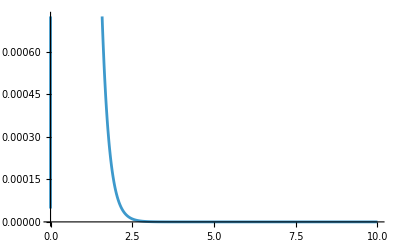

```mathematica
Plot[PjointPartEvalC[1.,t,1.], {t,0,10}](*44s w/o compilation, 55s with compilation*)
```

```mathematica
(*Numerical route*)
δ=10^-6;
FisherNum[ci_?NumericQ]:=NIntegrate[Module[{f0,fp,fm,dlog},
f0=PjointPartEval/. {t1->t1i,t2->t2i,c->ci};
fp=PjointPartEval/. {t1->t1i,t2->t2i,c->ci+δ};
fm=PjointPartEval/. {t1->t1i,t2->t2i,c->ci-δ};
(*central-difference derivative of log-pdf*)
dlog=(Log[fp]-Log[fm])/(2 δ);
dlog^2*f0],{t1i,0,100},{t2i,0,100},
Method->{"GlobalAdaptive"},
MaxRecursion->6];
```

```mathematica
FisherNum[1.]
```

0.153193

```mathematica
(*Symbolic route*)
d2LogPjointPartEval =D[Log[PjointPartEval ],{c,2}];
integrand = PjointPartEval *d2LogPjointPartEval ;(*0.4s*)
```

```mathematica
integrand/.{konb->kmax,kuon->kmax, koffu->kmax,kboff->kdl,kbon->kmin,konu->kmin,kuoff->kmax,c->1.,t1->1., t2->1.}(*1m*)
```

-0.00467655

```mathematica
integrandPartEval = integrand/.{konb->kmax,kuon->kmax, koffu->kmax,kboff->kdl,kbon->kmin,konu->kmin,kuoff->kmax};
```

```mathematica
compiledInt=Compile[{{t1,_Real},{t2,_Real},{c,_Real}},
Evaluate[integrand],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

```mathematica
compiledInt
```

```mathematica
integrandSimpl=Simplify[integrand];
```

```mathematica
-NIntegrate[integrandSimpl,{t1,0,∞},{t2,0,∞},
Method->"DoubleExponential", 
PrecisionGoal->8,
MinRecursion->5,
MaxRecursion->10]
```

0.000376928

```mathematica
Fcyc[c0_]:=Module[{intc},
intc =  Evaluate[integrand/.{c->c0,c2->0,γ->10,konb->kmax,kuon->kmax, koffu->kmax,kboff->kdl,kbon->kmin,konu->kmin,kuoff->kmax}];
-NIntegrate[intc,{t1,0,∞},{t2,0,∞},
Method->"DoubleExponential", 
PrecisionGoal->8,
MinRecursion->5,
MaxRecursion->10]
];
```

```mathematica
Fcyc[0.01]
```

0.230491

```mathematica
Simplify[With[{c=1.},Evaluate[integrand]]]
```

(ⅇ^(-4. t1-3.73205 t2) (-0.188818-0.187844 ⅇ^(3.4641 t2) (0.5-1. t2)^2+ⅇ^(6. t1+6.9282 t2) (0.0202131-0.0126484 t2)+ⅇ^(6.9282 t2) (0.000973313-0.000486656 t2)+ⅇ^(6. t1) (0.00326746+0.000908113 t2)+ⅇ^(3. t1+6.9282 t2) (-0.010654-0.0188748 t1-0.0515668 t1^2+0.00496202 t2)+ⅇ^(3. t1) (0.104576-0.262892 t1+0.19245 t1^2+0.0185185 t2)+0.0944088 t2+ⅇ^(6. t1+3.4641 t2) (0.0234805+0.0469611 t2+0.0939222 t2^2)+ⅇ^(3. t1+3.4641 t2) (0.0939222+0.704416 t1^2-0.657455 t2+0.939222 t2^2+t1 (-0.563533+1.6906 t2))))/(2.73205+0.267949 ⅇ^(3. t1)-0.196152 ⅇ^(3.4641 t2)+1. ⅇ^(3. t1+3.4641 t2))

```mathematica
Simplify[integrand]
```

```mathematica
pathList = {{1,3},{3,1},{1,5},{5,1},{4,5},{5,4}};

(*Mean first passage times*)
M2 = MeanFirstPassageTimes2[Q2];
meanTs = Table[M2[[pathList[[i,1]],pathList[[i,2]]]][[1]],{i,1,6}];

(*Variance of first passage times*)
V2 = VarianceFirstPassageTimes[Q2];
varTs = Table[V2[[pathList[[i,1]],pathList[[i,2]]]][[1]][[1]],{i,1,6}];
```

```mathematica
(*Laplace*)
F2= LaplaceTransformFPT[Q2,s];
laplaceTs = Table[F2[[pathList[[i,1]],pathList[[i,2]]]][[1]],{i,1,6}];

(*Check that mean Ton and var Ton from both methods agree*)
dF = Table[With[{s=0}, Evaluate[D[Fij, {s,1}]]],{Fij,laplaceTs}];
d2F = Table[With[{s=0}, Evaluate[D[Fij, {s,2}]]],{Fij,laplaceTs}];
```

```mathematica
varsLt = Table[d2F[[i]] - dF[[i]]^2,{i,1,6}];
```

```mathematica
Do[Assert[FullSimplify[-dF[[i]]] == FullSimplify[meanTs[[i]]]],{i,1,6}];
```

```mathematica
Do[Assert[FullSimplify[Expand[varsLt[[i]]]] == FullSimplify[Expand[varTs[[i]]]]],{i,1,6}];
```

```mathematica
(*Comparing with built-in functions*)
mproc1 = ContinuousMarkovProcess[1,Q2];
mproc3 = ContinuousMarkovProcess[3,Q2];
mproc4 = ContinuousMarkovProcess[4,Q2];
mproc5 = ContinuousMarkovProcess[5,Q2];
```

```mathematica
dist13 = FirstPassageTimeDistribution[mproc1,3];
dist15 = FirstPassageTimeDistribution[mproc1,5];

dist31 = FirstPassageTimeDistribution[mproc3,1];
dist41 = FirstPassageTimeDistribution[mproc4,1];
dist51 = FirstPassageTimeDistribution[mproc5,1];
distToff = FirstPassageTimeDistribution[mproc1,{3,4,5}];

meanTonBuiltin = (ss2[[2]]*Q2[[2,3]]*Mean[dist31]+ ss2[[1]]*Q2[[1,4]]*Mean[dist41]+ ss2[[6]]*Q2[[6,5]]*Mean[dist51])/(ss2[[2]]*Q2[[2,3]]+ss2[[6]]*Q2[[6,5]]+ss2[[1]]*Q2[[1,4]]);
FullSimplify[meanTonBuiltin]
```

(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb (koffu+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+konu kuon γ (konb+kuoff γ)+c2 kboff konb (koffu+kuon γ)))/(koffu kuon γ (c kboff konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff konb+konu (konb+kuoff γ))))

```mathematica
(*1,1,1,1e-4,1,0,0*)
With[{c=12.,c2=0.001,γ=2,kboff=0.0502,konb=0.2,kuon=0.05,kbon=0.00001,koffu=5,kuoff=0,konu=0},Evaluate[meanTonBuiltin]]
```

20.1996

```mathematica
20.199646756105324
```

```mathematica
FullSimplify[meanTonLt]
```

meanTonLt

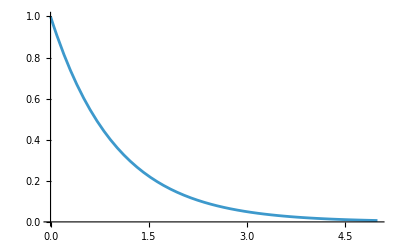

```mathematica
Plot[With[{c=1,c2=1,kboff=1,konb=1,kuon=1,kbon=1,koffu=1,kuoff=1,konu=1, γ=1},Evaluate[PDF[distToff,t0]]],{t0,0,5}]
```

```mathematica
With[{c=1,c2=1,kboff=1,konb=1,kuon=1,kbon=1,koffu=1,kuoff=1,konu=1, γ=1},Evaluate[PDF[distToff,5.]]]
```

0.00673795

```mathematica
0.006737946999085455
```

```mathematica
meanToffBuiltin = FullSimplify[Mean[distToff]]
```

(c kboff (konb+kuoff γ)+(konb+kuoff) (c2 kboff+konb+kuoff γ))/(c kboff konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff konb+konu (konb+kuoff γ)))

```mathematica
With[{c=50.,c2=0.00001,γ=1,kboff=0.0502,konb=0.2,kuon=0.05,kbon=0.00001,koffu=5,kuoff=0,konu=0},Evaluate[meanTonBuiltin]]
```

20.202

```mathematica
20.2020000004
```

```mathematica
FullSimplify[meanToffLt]
```

((c kboff+konb+kuoff) (konb+kuoff γ)+c kboff (konb+kuoff) ω)/(konu (konb+kuoff) (konb+kuoff γ)+c kboff konb (konb+kuoff γ+(konb+kuoff) ω))

```mathematica
(*evaluating at the beginning*)
meanTonLtNoω = Simplify[With[{ω=0,konu=0},Evaluate[meanTonLt]],assum]
```

(c kbon+koffu+kuon)/(koffu kuon)

```mathematica
cHatOnSymNoω = FullSimplify[c/.Solve[meanTonLtNoω==sampleTon,c][[1]],assum]
```

-(koffu+kuon-koffu kuon sampleTon)/kbon

```mathematica
dcHatOnSymNoω = FullSimplify[D[cHatOnSymNoω,sampleTon],assum]
```

(koffu kuon)/kbon

```mathematica
FullSimplify[With[{sampleTon = meanTonLtNoω},Evaluate[dcHatOnSymNoω]],assum]
```

(koffu kuon)/kbon

```mathematica
(*evaluating at the end*)
cHatOnSymSimpl = Simplify[With[{ω=0,kuoff=0,koffu=1,kbon=1,kboff=1,kuon=1},Evaluate[cHatOnSym]],assum]
```

1/2 (-2-konu+sampleTon-√(konu^2+(-2+sampleTon)^2+2 konu sampleTon))

```mathematica
meanTonSimpl = Simplify[With[{ω=0,kuoff=0,koffu=1,kbon=1,kboff=1,kuon=1},Evaluate[meanTonLt]]]
```

(c^2+konu+c (2+konu))/(c+konu)

```mathematica
Simplify[c/.Solve[meanTonSimpl==sampleTon,c][[2]],assum]
```

1/2 (-2-konu+sampleTon+√(konu^2+(-2+sampleTon)^2+2 konu sampleTon))

```mathematica
Simplify[With[{sampleTon=meanTonSimpl},Evaluate[%]],assum]
```

c

```mathematica
dcHatOnSym = Simplify[D[cHatOnSym,sampleTon],assum];
Simplify[With[{ω=0,kuoff=0,koffu=1,kbon=1,kboff=1,kuon=1},Evaluate[dcHatOnSym]],assum]
```

(2-konu-sampleTon+√(konu^2+(-2+sampleTon)^2+2 konu sampleTon))/(2 √(konu^2+(-2+sampleTon)^2+2 konu sampleTon))

```mathematica
dcHatOnSymEndEval = Simplify[With[{sampleTon=meanTonLt},Evaluate[dcHatOnSym]],assum];
```

```mathematica
Simplify[With[{ω=0,kuoff=0,koffu=1,kbon=1,kboff=1,kuon=1},Evaluate[dcHatOnSymEndEval]]]
```

konu/(c^2+konu+2 c konu+konu^2)

```mathematica
(*Computing the exact MLE variance*)
FOn=(ss2[[2]]*Q2[[2,3]]*F31+ ss2[[1]]*Q2[[1,4]]*F41+ ss2[[6]]*Q2[[6,5]]*F51)/(ss2[[2]]*Q2[[2,3]]+ss2[[6]]*Q2[[6,5]]+ss2[[1]]*Q2[[1,4]]);
FOnNoω = Simplify[With[{ω=0,kuoff=0},Evaluate[FOn]],{}]
```

Clear::wrsym: Symbol All is Protected.

(koffu (c kboff kuon (s2+kuon γ)+(kuon+s2) (c2 kboff kuon γ+konu (s2+kuon γ))))/((c kboff+c2 kboff+konu) (c2 kbon s2 (kuon+s2)+(koffu (kuon+s2)+s2 (c kbon+kuon+s2)) (s2+kuon γ)))

```mathematica
(*-4 koffu kuon+(c kbon+koffu+kuon)^2*) (*c^2 kbon^2+(koffu-kuon)^2+2 c kbon (koffu+kuon)*)
(*{D==-4 koffu kuon+(c kbon+koffu+kuon)^2,B==c kbon+koffu+kuon,A==koffu kuon}*)
POnNow[c] := Simplify[InverseLaplaceTransform[FOnNoω,s2,t2]]
```

```mathematica
POnNow[c]
```

```mathematica
FullSimplify[POnNow[c],{D==-4 koffu kuon+(c kbon+koffu+kuon)^2,B==c kbon+koffu+kuon,A==koffu kuon}]
```

(ⅇ^(-1/2 (B+√D) t2) ((B+√D+(-B+√D) ⅇ^(√D t2)) koffu konu+2 A (-1+ⅇ^(√D t2)) (c kboff+konu)))/(2 √D (c kboff+konu))

```mathematica
Expand[%]
```

-(A c ⅇ^(-1/2 (B+√D) t2) kboff)/(√D (c kboff+konu))+(A c ⅇ^(-1/2 (B+√D) t2+√D t2) kboff)/(√D (c kboff+konu))-(A ⅇ^(-1/2 (B+√D) t2) konu)/(√D (c kboff+konu))+(A ⅇ^(-1/2 (B+√D) t2+√D t2) konu)/(√D (c kboff+konu))+(ⅇ^(-1/2 (B+√D) t2) koffu konu)/(2 (c kboff+konu))+(B ⅇ^(-1/2 (B+√D) t2) koffu konu)/(2 √D (c kboff+konu))+(ⅇ^(-1/2 (B+√D) t2+√D t2) koffu konu)/(2 (c kboff+konu))-(B ⅇ^(-1/2 (B+√D) t2+√D t2) koffu konu)/(2 √D (c kboff+konu))

```mathematica
d2POnNow = FullSimplify[D[Log[POnNow[c]],{c,2}],{D==-4 koffu kuon+(c kbon+koffu+kuon)^2,B==c kbon+koffu+kuon,A==koffu kuon}]
```

$Aborted

```mathematica
integrand = FullSimplify[d2POnNow*POnNow[c],{D==-4 koffu kuon+(c kbon+koffu+kuon)^2,B==c kbon+koffu+kuon,A==koffu kuon}]
```

-(A ⅇ^(-1/2 (B+√D) t2) (-1+ⅇ^(√D t2)) kbon^2 (-4 (8 A+D)+8 A √D t2 Coth[(√D t2)/2]+D (4 A+D) t2^2 Csch[(√D t2)/2]^2))/(4 D^(5/2))

```mathematica
Simplify[FoffOn]
```

(koffu (c kboff konb kuon (konb+s1+kuoff γ) (s2+kuon γ)+(konb+kuoff+s1) (kuon+s2) (c2 kboff konb kuon γ+konb konu (s2+kuon γ)+konu (s1+kuoff γ) (s2+kuon γ))))/((c2 kbon s2 (kuon+s2)+(koffu (kuon+s2)+s2 (c kbon+kuon+s2)) (s2+kuon γ)) (c kboff (konb+s1) (konb+s1+kuoff γ)+(konb+kuoff+s1) (c2 kboff (konb+s1)+(konu+s1) (konb+s1+kuoff γ))))